# Trust Region SubProblem

We are going to need to repeatedly approximately solve
	argmin_(√(p.B.p)≤Δ)(g.p+0.5p.H.p)
in our algorithms where g∈ℝ^n with B and H n×n symmetric matrices with B positive definite. A simple accurate algorithm is described in

Adachi, S., Iwata, S., Nakatsukasa, Y., & Takeda, A.
Solving the trust-region subproblem by a generalized eigenvalue problem.
SIAM Journal on Optimization 27.1 (2017): 269-291.

## Trust Region Newton Algorithm

Here is a single step of a plausible algorithm.  It is a Trust Region Newton algorithm with a radius Δ_k spherical trust region √(p.B.p)=√(p.I.p)≤Δ_k.

	g=df[x_k]; H=ddf[x_k]; B=Id;
	p_k=argmin_(||p||≤Δ_k)(g.p+0.5p.H.p)
	x_(k+1)=x_k+p_k

You could initialize this with a random x_0 and end when ||g|| was less than some tolerance.  The only thing that is not specified here is how to choose/update the trust region radius Δ_k

## Adachi Algorithm

We need to build a test problem.

```mathematica
{n,Δ}={23,0.1};
{A,B}=RandomReal[{-1,1},{2,n,n}];
B=B.Bᵀ;A=A+Aᵀ;
{g,p0}=RandomReal[{-1,1},{2,n}];
f[p_List]:=g.p+0.5 p.A.p
c[p_]:=Δ^2-p.B.p
{val,sub}=FindMinimum[{f[p],c[p]≥0},{p, p0}];
{f[p],c[p]}/.sub
```

{-1.56234,-8.318×10^-9}

The algorithm is pretty simple

```mathematica
{M0,M1}=Map[ArrayFlatten,{({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}}),-({{0, B}, {B, 0}})}];
{{λMin,y1y2Min},{λMax,y1y2Max}}=Chop[Sort[Eigensystem[{M0,M1}]ᵀ]⟦{-1,1}⟧];
{y1Min,y2Min}=Partition[y1y2Min,n];
{y1Max,y2Max}=Partition[y1y2Max,n];
p1Min=-Sign[g.y2Min]Δ y1Min/(√(y1Min.B.y1Min));
p1Max=-Sign[g.y2Max]Δ y1Max/(√(y1Max.B.y1Max));
{f[p1Min],c[p1Min]}
{f[p1Max],c[p1Max]}
```

{-1.56234,-1.09808×10^-15}

{7865.96,-6.57823×10^-12}

## Project Two Plan

Our second project is to compare the full TRS algorithm to some very simple approximations on a set of plausible problems. Our first approximation involves ignoring the possibility of the hard case and approximating the eigenvalue problem by a few steps of the power method.!

The article below compares the full TRS algorithm to other “fancy” algorithms.

A COMPARISON OF EIGENVALUE-BASED ALGORITHMS AND THE GENERALIZED LANCZOS TRUST-REGION ALGORITHM FOR SOLVING THE TRUST-REGION SUBPROBLEM∗ ZHONGXIAO JIA AND FA WANG.

## Project Three Plan

Our third project is to compare use the TRS algorithm to implement an interior algorith for the box constrained optimization problem. 
	argmin_(l<x<u)f(x)
where the lower bound l∈ℝ^n and the upper bound u∈ℝ^n and the condition means
	Ω={x∈ℝ^n: l_i≤x_i≤u_i} 
for i=1,2,…,n.   The interpretation if one or more of the l_i=-∞ and/or one or more of the u_i=+∞ is obvious.

All we need to do is build an axis aligned ellipse E centered at the current iterate x satisfying 
	S⊂Ω∩ℬ_Δ(x_k)
where 
	ℬ_Δ(c)={x∈ℝ^n: ||x-c||≤Δ}.
The key here is that the matrix  B defining 
	S_(B,c)={x∈ℝ^n: √((x-c).B.(x-c))≤1}
needs to be cheap to build and operate with.

For c∈Ω compute r_i=min(c_i-l_i, u_i-c_i,Δ).  In words r_i is the smaller of the distance to the boundary and the trust region radius and define 
	B=DiagonalMatrix[{r_1^-2,r_2^-2,…,r_n^-2}].

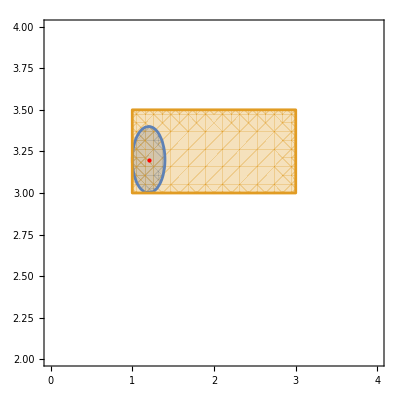

```mathematica
l={1,3}; u={3, 3.5}; Δ=0.3;
c={1.2,3.2};
r=Table[ Min[c⟦i⟧-l⟦i⟧,u⟦i⟧-c⟦i⟧,Δ],{i,2}];
B=DiagonalMatrix[1/r^2];
RegionPlot[{
√(({x1,x2}-c).B.({x1,x2}-c))≤1,
And[l⟦1⟧<=x1≤u⟦1⟧,l⟦2⟧<=x2≤u⟦2⟧ ]
},{x1,0,4},{x2,2,4},
Epilog->{Red,Point[c]}]
```

```mathematica
l={1,3,2}; u={3, 3.5,4}; Δ=0.3;
c={1.2,3.2,3};
r=Table[ Min[c⟦i⟧-l⟦i⟧,u⟦i⟧-c⟦i⟧,Δ],{i,3}];
B=DiagonalMatrix[1/r^2];
RegionPlot3D[{
√(({x1,x2,x3}-c).B.({x1,x2,x3}-c))≤1,
And[l⟦1⟧<=x1≤u⟦1⟧,l⟦2⟧<=x2≤u⟦2⟧ ,l⟦3⟧<=x3≤u⟦3⟧]
},{x1,0,4},{x2,2,4},{x3,1,6},
PlotStyle->{Opacity[1],Opacity[0.1]},
PlotPoints->50]
```

-Graphics3D-

## Trust Region Interior Point Newton Algorithm for bound constrained optimization is

g=df[x_k]; H=ddf[x_k]; B_k as defined above.
	p_k=argmin_(√(p.B_k.p)≤Δ_k)(g.p+0.5p.H.p)
	x_(k+1)=x_k+p_k

You could initialize this with a random x_0 and end when the KKT equations are satisfied to some tolerance. The only thing that is not specified here is how to choose/update the trust region radius Δ_k